# Initialization

```mathematica
$HistoryLength=1;
(*In development the package may not be installed correctly, so add the right path just in case*)
With[{pfn=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..",".."}]},
If[!MemberQ[$Path,pfn], PrependTo[$Path,pfn]];
];

Needs["Developer`"]
Needs["DiffusiveDynamics`"]
(*Load the data on paralle Kernels*)
With[{path=$Path},
ParallelEvaluate[

$Path=path;(*add to the path of parallel Kernels*)
Needs["Developer`"];
Needs["DiffusiveDynamics`"];
$HistoryLength=1;
]];
$VerbosePrint=True;
$VerboseLevel=1;
```

# Generate Diffusion

## Initial condition

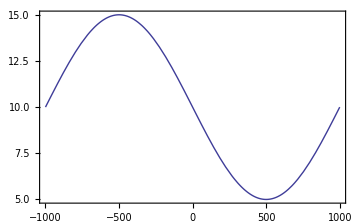
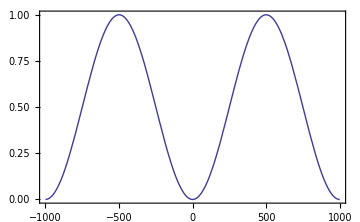

```mathematica
STEPS=10^5;
STEP=1;
CELLRANGE=1000.;
ClearAll[DIFF,ENERGY];
DIFF=Compile[{{x, _Real}},5Sin[(x+CELLRANGE)/CELLRANGE*π]+10];
(*energija v enotah kT*)
ENERGY=Compile[{{x, _Real}},Sin[(x+CELLRANGE)/CELLRANGE*π]^2];
(*ENERGY[x_]:=-Cos[x/CELLRANGE*π]+Integrate[Log[Exp[Cos[2t]]],{t,-π,π}];*)
KT=1.;
{Plot[DIFF[x],{x,-CELLRANGE,CELLRANGE},PlotRange->{0,All},Frame->True,ImageSize->Medium],
Plot[ENERGY[x],{x,-CELLRANGE,CELLRANGE},PlotRange->{0,All},Frame->True,ImageSize->Medium]}
```

## Generate in serial

0.088

{1,100001,2}

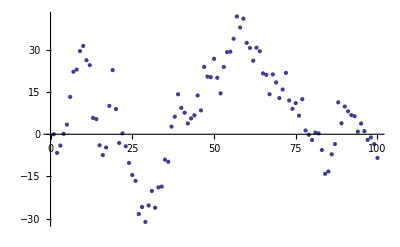

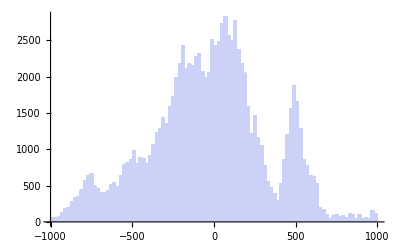

```mathematica
$VerbosePrint=False;
$VerboseLevel=5;
rwData={GenerateDiffusionTrajectory1D[STEPS=10^5,DIFF,ENERGY,KT,STEP,{-CELLRANGE,CELLRANGE}]};//AbsoluteTiming//First
Dimensions@rwData
rwData⟦1,1;;100⟧;
ListPlot[rwData[[1,1;;100]]]
Histogram[rwData⟦1,All,2⟧]
```

## Generate in “parallel”

0.86705

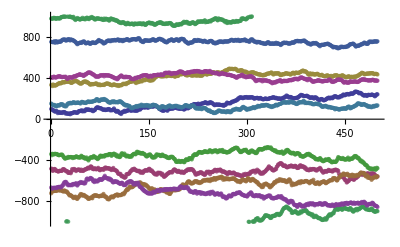

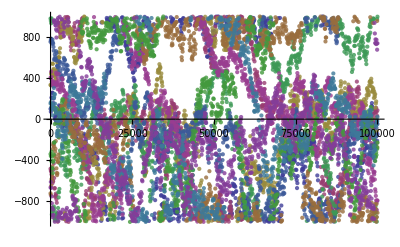

```mathematica
$VerbosePrint=False;
$VerboseLevel=5;
rwData=ParallelGenerateDiffusionTrajectory1D[STEPS=10^6,DIFF,ENERGY,KT,STEP=2,{-CELLRANGE,CELLRANGE},"ProcessCount"->10,"InitialPositions"->{100}];//AbsoluteTiming//First
ListPlot[rwData[[All,1;;500]],Joined->False,PlotStyle->Opacity@0.8]
ListPlot[rwData[[All,1;;-1;;100]],Joined->False,PlotStyle->Opacity@0.8]
```

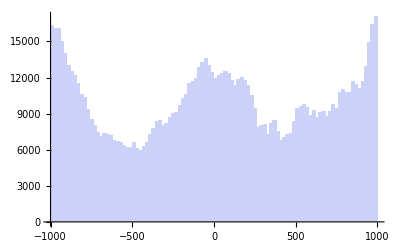

```mathematica
Histogram[Flatten@rwData⟦All,All,2⟧,PerformanceGoal->"Speed"]
```

# Analyze diffusion

## One bin

```mathematica
$VerbosePrint=True;
$VerboseLevel=5;
strides={1,10,50,100};
strides={1};
GetDiffusionInBin1D[rwData,STEP,{0,200},{-CELLRANGE,CELLRANGE},"Strides"->strides]//AbsoluteTiming
```

{43.25147,{{Dx→8.31598,ux→0.00553264,sx→5.76749,PValue→0.000838272,IsNormal→False,xMinWidth→34.6049,Stride→1,x→100,xWidth→200,StepsInBin→119611,dt→2,StepsHistogram→Null}}}

## Multiple bins

```mathematica
$VerbosePrint=False;
$VerboseLevel=1;
strides={1};
strides={1,10,50,100};
strides=Range@50;
binspec={-1000,1000,200};
diffs=GetDiffusionInBins1D[rwData,STEP,binspec,"Strides"->strides];//AbsoluteTiming//First
(*returns bins, strides,diff data*)
```

32.20384

```mathematica
Dimensions@diffs
diffs[[All,2]]
```

{10,50,12}

{{Dx→11.2658,ux→-0.0122733,sx→9.49351,PValue→0.432524,IsNormal→True,xMinWidth→56.9611,Stride→2,x→-900,xWidth→200,StepsInBin→123717,dt→2,StepsHistogram→Null},{Dx→13.6275,ux→-0.018924,sx→10.4413,PValue→0.828141,IsNormal→True,xMinWidth→62.6476,Stride→2,x→-700,xWidth→200,StepsInBin→82731,dt→2,StepsHistogram→Null},{Dx→14.497,ux→-0.00923837,sx→10.7692,PValue→0.000559237,IsNormal→False,xMinWidth→64.6154,Stride→2,x→-500,xWidth→200,StepsInBin→80634,dt→2,StepsHistogram→Null},{Dx→13.489,ux→-0.00824259,sx→10.3881,PValue→0.589555,IsNormal→True,xMinWidth→62.3284,Stride→2,x→-300,xWidth→200,StepsInBin→120160,dt→2,StepsHistogram→Null},{Dx→11.2796,ux→-0.0131922,sx→9.49931,PValue→0.156209,IsNormal→True,xMinWidth→56.9959,Stride→2,x→-100,xWidth→200,StepsInBin→154840,dt→2,StepsHistogram→Null},{Dx→8.37781,ux→-0.0203016,sx→8.18673,PValue→0.0556525,IsNormal→True,xMinWidth→49.1204,Stride→2,x→100,xWidth→200,StepsInBin→130717,dt→2,StepsHistogram→Null},{Dx→6.01502,ux→-0.0393347,sx→6.93687,PValue→0.0330865,IsNormal→False,xMinWidth→41.6212,Stride→2,x→300,xWidth→200,StepsInBin→75624,dt→2,StepsHistogram→Null},{Dx→4.89772,ux→-0.0353471,sx→6.25954,PValue→0.214684,IsNormal→True,xMinWidth→37.5572,Stride→2,x→500,xWidth→200,StepsInBin→43272,dt→2,StepsHistogram→Null},{Dx→6.09228,ux→-0.0249876,sx→6.98128,PValue→0.208711,IsNormal→True,xMinWidth→41.8877,Stride→2,x→700,xWidth→200,StepsInBin→71337,dt→2,StepsHistogram→Null},{Dx→8.36332,ux→-0.0155953,sx→8.17964,PValue→0.00884268,IsNormal→False,xMinWidth→49.0779,Stride→2,x→900,xWidth→200,StepsInBin→119674,dt→2,StepsHistogram→Null}}

## Draw target and calculated value

Draw xMinWidth vs bin width

1

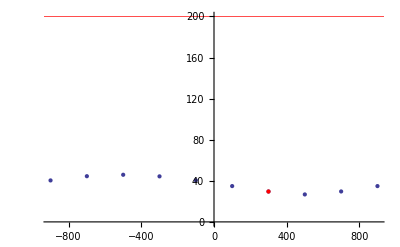

```mathematica
s=1
vals=GetValues[{"x","xMinWidth","IsNormal"},diffs[[All,s]]];
allVals=vals[[All,{1,2}]];
nonNormalVals=Select[vals,Not[#[[3]]]&][[All,{1,2}]];
lp1=ListPlot[allVals,GridLines->{{},{binspec⟦3⟧}},GridLinesStyle->Directive[Red,Thick],PlotRange->{0,Max[binspec⟦3⟧,vals[[All,2]]]}];
If[Length@nonNormalVals>0,lp2=ListPlot[nonNormalVals,PlotStyle->Red];,lp2=Graphics[]];
Show[lp1,lp2]
```

View different strides

```mathematica
Manipulate[
targetPlot=Plot[DIFF[x],{x,-CELLRANGE,CELLRANGE},PlotRange->{0,All},Frame->True,ImageSize->Medium];
recalcDiffPlot=ListPlot[GetValues[{"x","Dx"},diffs[[All,s]]]];
diffPlot=Show[{targetPlot,recalcDiffPlot}];
vals=GetValues[{"x","xMinWidth"},diffs[[All,s]]];
vals=GetValues[{"x","xMinWidth","IsNormal"},diffs[[All,s]]];
allVals=vals[[All,{1,2}]];
nonNormalVals=Select[vals,Not[#[[3]]]&][[All,{1,2}]];
lp1=ListPlot[allVals,GridLines->{{},{binspec⟦3⟧}},GridLinesStyle->Directive[Red,Thick],PlotRange->{0,Max[binspec⟦3⟧,vals[[All,2]]]},ImageSize->Medium];
If[Length@nonNormalVals>0,lp2=ListPlot[nonNormalVals,PlotStyle->Red];,lp2=Graphics[]];
minSizePlot=Show[lp1,lp2];
{strides[[s]]
,diffPlot
,minSizePlot}
,{{s,1},1,Length@strides,1}]
```

# Misc. (easier git handling)

```mathematica
(*For easier storage in Git*)
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False];FrontEndTokenExecute["DeleteGeneratedCells"];
```

```mathematica
(*Auto delete output on close*)
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndTokenExecute["DeleteGeneratedCells"]}];
```